```mathematica
With[{p=2,q=3},
ArrayPlot[Table[PadLeft[IntegerDigits[Distance[p^i,q],q],100],{i,100,200}]]
]
```

-Graphics-

```mathematica
Histogram [
Flatten@With[{p=2,q=3},
Map[
#[[2]]-#[[1]]&,
ParallelTable[FirstNonGood[2^i,q],{i,1,200000}]
]
], PlotRange->All
]
```

$Aborted

```mathematica
DistributeDefinitions[FirstNonGood,Distance]
```

```mathematica
a=Sum[2^j,{j,1,500,500}]
```

2

```mathematica
Table[
ArrayPlot[Transpose[Map[
PadRight[#,30]&,
With[{p=2,q=3},
Map[
IntegerDigits[#,q]&,
ParallelTable[
With[
{v=2^i},
v+Distance[v,q]],{i,step*100,(step+1)*100}]
]
]
]],ImageSize->1200,Mesh->Full],
{step,0,10}
]
```

ArrayPlot::mesh: Value of option Mesh -> Full is not All, None, n, or a valid list of mesh specifications; using All instead.

General::stop: Further output of ArrayPlot will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
v=With[
{p=2,q=3},
Monitor[
Map[Length,
Select[
Split[
Table[
With[
{v=2^i},
IntegerDigits[v+Distance[v,q],q][[2]]
],
{i,50,10000}
],Equal
],
#[[1]]≠1&
]
]
,i]
]
```

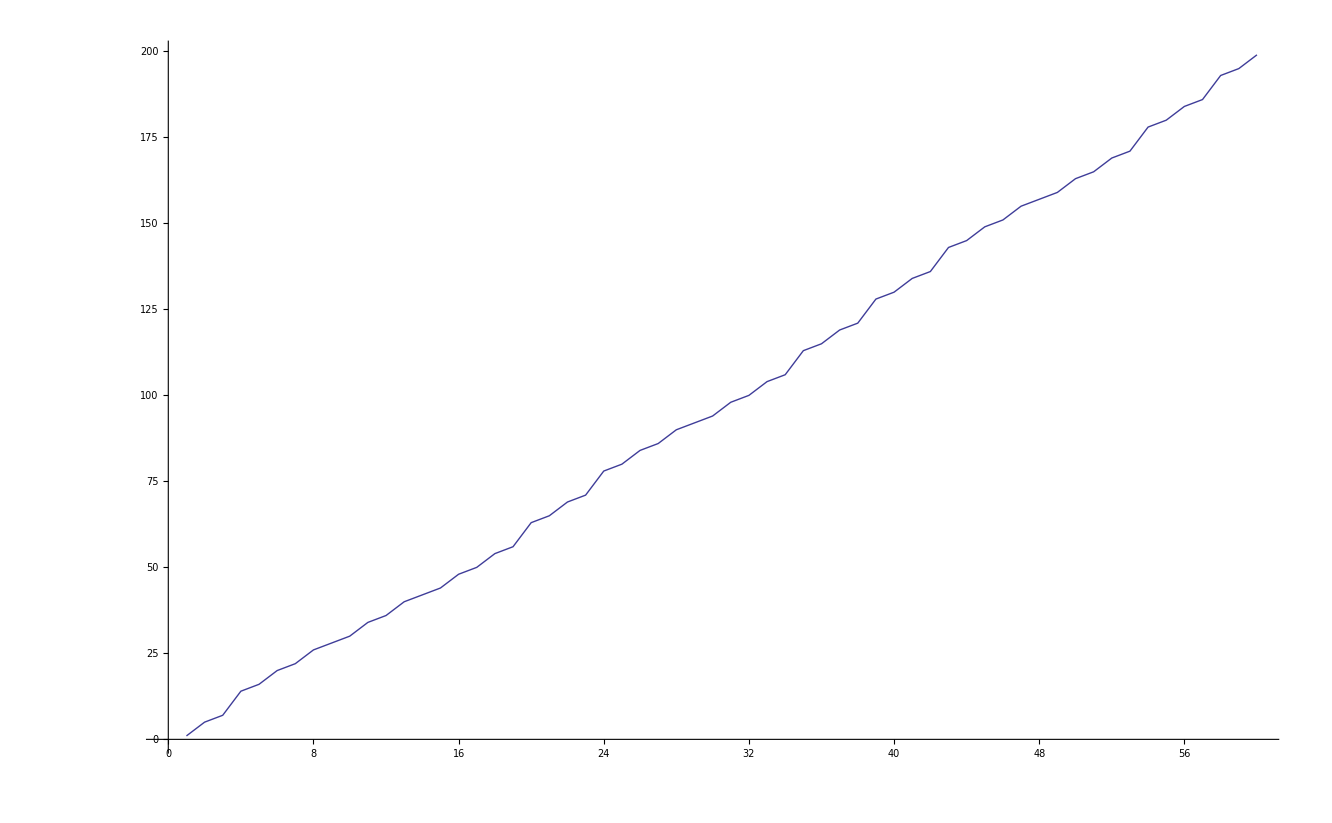

```mathematica
ListLinePlot[Accumulate[Take[v,60]]]
```